## Pregunta 1

```mathematica
$Assumptions={R∈Reals,R>0,l∈Reals,l>0,l>R,ρ∈Reals,ρ>0,ρ<R};
```

```mathematica
Inercia=(3m)/(π R^2 l)∫_0^l ∫_(-R z/l)^(R z/l) ∫_(-√((R z/l)^2-y^2))^(√((R z/l)^2-y^2)) ({{y^2+z^2, -x y, -x z}, {-x y, x^2+z^2, -y z}, {-x z, -y z, x^2+y^2}})ⅆxⅆyⅆz//FullSimplify
```

{{3/20 m (4 l^2+R^2),0,0},{0,3/20 m (4 l^2+R^2),0},{0,0,(3 m R^2)/10}}

```mathematica
Ω=({{0}, {θ̇}, {l/R θ̇}})
```

{{0},{θ̇},{(l θ̇)/R}}

```mathematica
(1/2(Ωᵀ.Inercia.Ω)//FullSimplify)[[1]][[1]]
```

3/40 m (6 l^2+R^2) (θ̇)^2

```mathematica
yCM=(∫_0^l ∫_0^(R z/l) ∫_0^(2π) z rⅆθⅆrⅆz)/(∫_0^l ∫_0^(R z/l) ∫_0^(2π) rⅆθⅆrⅆz)
```

(3 l)/4

## Pregunta 2

```mathematica
θ[ρ_]:=2HeavisideTheta[R-ρ] ArcSin[ρ/R]
```

```mathematica
$Assumptions={R∈Reals,R>0,r∈Reals,r>0,ρ∈Reals,ρ>0,r>0,w>0,e>0};
```

α=ρ/R,ρ=Rα

```mathematica
1/π∫_((r w)/R)^1 θ[R α]/(√(R^2 α^2-r^2 w^2))Rⅆα
```

-HeavisideTheta[1-(r w)/R] Log[R/(R+√(R^2-r^2 w^2))]

```mathematica
Solve[w==Exp[-Log[R/(R+√(R^2-r^2 w^2))]],w]
```

{{w→ConditionalExpression[(2 R^2)/(r^2+R^2), r<R]}}

```mathematica
Solve[{√(1-U/e)==(2 R^2)/(r^2+R^2),r<R},U]//FullSimplify
Solve[√(1-U/e)==1,U]//FullSimplify
```

{{U→ConditionalExpression[(e (r^4+2 r^2 R^2-3 R^4))/((r^2+R^2)^2), r<R]}}

{{U→0}}

```mathematica
(r^4+2 r^2 R^2-3 R^4)/((r^2+R^2)^2)-((r^2+R^2)^2-4 R^4)/((r^2+R^2)^2)//Simplify
```

0

```mathematica
(r^4+2 r^2 R^2-3 R^4)/((r^2+R^2)^2)-(1-4/((1+(r/R)^2)^2))//Simplify
```

0

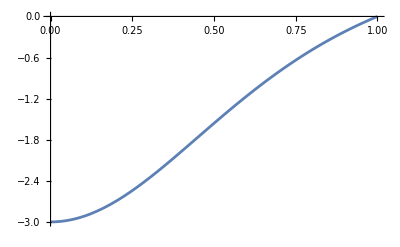

```mathematica
Plot[1-4 1^4/((r^2+1^2)^2),{r,0,1}]
```

```mathematica
ρ[θ_]:=R Sin[θ/2]
```

```mathematica
ρ[θ0]
```

R Sin[θ0/2]

```mathematica
D[ρ[θ0], θ0]
```

1/2 R Cos[θ0/2]

```mathematica
ρ[θ0]/Sin[θ0] Abs[D[ρ[θ0], θ0]]//FullSimplify
```

R^2/(4 Sign[Cos[θ0/2]])

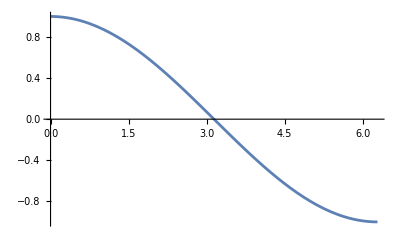

```mathematica
Plot[Cos[θ/2],{θ,0,2π}]
```